# TRABAJO REPRODUCIBLE

```mathematica
ClearAll["Global'*"]
```

```mathematica
?ParentDirectory
```

```mathematica
?NotebookDirectory
```

```mathematica
base=ParentDirectory[NotebookDirectory[]]
```

/home/luis/Documentos

```mathematica
archivo=FileNameJoin[{base,"mediciones_llenado.csv"}] (* solo se usa para formar un string uniendo todo tu path en otro string *)
```

/home/luis/Documentos/mediciones_llenado.csv

```mathematica
raw=Import[archivo,"CSV"] (*REQUIERE FORZOSAMENTE MAYUSCULAS EN EL SEGUNDO ARGUMENTO PARA QUE EXTRAIGA TIPO DE ARCHIVO*)
```

{{n,peso_g},{1,248.9},{2,250.3},{3,247.3},{4,252.},{5,250.9},{6,249.6},{7,249.6},{8,250.4},{9,249.6},{10,249.7},{11,251.},{12,250.7},{13,249.9},{14,249.9},{15,250.2},{16,249.1},{17,249.4},{18,250.8},{19,249.8},{20,248.1},{21,249.3},{22,250.9},{23,249.7},{24,249.8},{25,250.9},{26,252.6},{27,249.},{28,251.9},{29,248.3},{30,250.2},{31,248.4},{32,251.9},{33,251.2},{34,251.6},{35,248.8},{36,251.},{37,249.3},{38,256.3},{39,250.7},{40,251.2},{41,250.3},{42,249.1},{43,248.8},{44,252.},{45,250.8},{46,251.},{47,253.1},{48,248.9},{49,253.6},{50,254.4},{51,252.3},{52,251.2},{53,249.1},{54,251.4},{55,249.4},{56,250.},{57,249.6},{58,250.4},{59,251.8},{60,249.2},{61,248.6},{62,248.6},{63,248.6},{64,248.},{65,248.7},{66,251.8},{67,249.2},{68,250.4},{69,248.3},{70,250.2},{71,249.1},{72,250.5},{73,254.7},{74,250.7},{75,253.1},{76,252.1},{77,251.3},{78,250.6},{79,253.3},{80,251.3},{81,253.6},{82,250.5},{83,251.6},{84,243.6},{85,252.},{86,249.8},{87,250.6},{88,251.2},{89,250.3},{90,252.4},{91,252.3},{92,248.8},{93,249.},{94,249.7},{95,251.7},{96,254.3},{97,251.},{98,251.9},{99,250.},{100,250.}}

```mathematica
First[raw]
```

{n,peso_g}

```mathematica
MatrixForm[raw]
```

(n | peso_g
1 | 248.9
2 | 250.3
3 | 247.3
4 | 252.
5 | 250.9
6 | 249.6
7 | 249.6
8 | 250.4
9 | 249.6
10 | 249.7
11 | 251.
12 | 250.7
13 | 249.9
14 | 249.9
15 | 250.2
16 | 249.1
17 | 249.4
18 | 250.8
19 | 249.8
20 | 248.1
21 | 249.3
22 | 250.9
23 | 249.7
24 | 249.8
25 | 250.9
26 | 252.6
27 | 249.
28 | 251.9
29 | 248.3
30 | 250.2
31 | 248.4
32 | 251.9
33 | 251.2
34 | 251.6
35 | 248.8
36 | 251.
37 | 249.3
38 | 256.3
39 | 250.7
40 | 251.2
41 | 250.3
42 | 249.1
43 | 248.8
44 | 252.
45 | 250.8
46 | 251.
47 | 253.1
48 | 248.9
49 | 253.6
50 | 254.4
51 | 252.3
52 | 251.2
53 | 249.1
54 | 251.4
55 | 249.4
56 | 250.
57 | 249.6
58 | 250.4
59 | 251.8
60 | 249.2
61 | 248.6
62 | 248.6
63 | 248.6
64 | 248.
65 | 248.7
66 | 251.8
67 | 249.2
68 | 250.4
69 | 248.3
70 | 250.2
71 | 249.1
72 | 250.5
73 | 254.7
74 | 250.7
75 | 253.1
76 | 252.1
77 | 251.3
78 | 250.6
79 | 253.3
80 | 251.3
81 | 253.6
82 | 250.5
83 | 251.6
84 | 243.6
85 | 252.
86 | 249.8
87 | 250.6
88 | 251.2
89 | 250.3
90 | 252.4
91 | 252.3
92 | 248.8
93 | 249.
94 | 249.7
95 | 251.7
96 | 254.3
97 | 251.
98 | 251.9
99 | 250.
100 | 250.)

{248.9,250.3,247.3,252.,250.9,249.6,249.6,250.4,249.6,249.7,251.,250.7,249.9,249.9,250.2,249.1,249.4,250.8,249.8,248.1,249.3,250.9,249.7,249.8,250.9,252.6,249.,251.9,248.3,250.2,248.4,251.9,251.2,251.6,248.8,251.,249.3,256.3,250.7,251.2,250.3,249.1,248.8,252.,250.8,251.,253.1,248.9,253.6,254.4,252.3,251.2,249.1,251.4,249.4,250.,249.6,250.4,251.8,249.2,248.6,248.6,248.6,248.,248.7,251.8,249.2,250.4,248.3,250.2,249.1,250.5,254.7,250.7,253.1,252.1,251.3,250.6,253.3,251.3,253.6,250.5,251.6,243.6,252.,249.8,250.6,251.2,250.3,252.4,252.3,248.8,249.,249.7,251.7,254.3,251.,251.9,250.,250.}

100

<|n→100,media→250.5,desv→1.75706,min→243.6,max→256.3|>

/home/luis/Documentos/evidencias

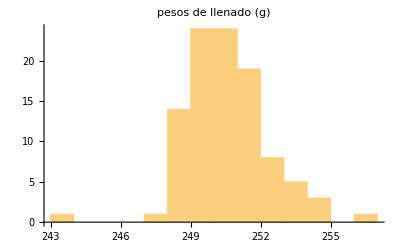

/home/luis/Documentos/evidencias/hist_pesos.png

```mathematica
pesos=raw[[2;;,2]]
Length[pesos]
resumen[v_List] := <|"n" -> Length[v], "media" -> Mean[v],
"desv" -> StandardDeviation[v], "min" -> Min[v], "max" -> Max[v]|>
resumen[pesos]
carpeta=FileNameJoin[{base, "evidencias"}]
If[!DirectoryQ[carpeta],CreateDirectory[carpeta]] (*cambia a falso !*)
g=Histogram[pesos,{1},PlotLabel-> "pesos de llenado (g)"]
Export[FileNameJoin[{carpeta, "hist_pesos.png"}], g] (* ya viene dentro de export tienes que escribir el nombre completo Export[aqui va ruta ya con el nombre de lo que exportaras,lo que exportas]*)
```

```mathematica
a={{1, 10.5, 20.1}, {2, 30.2, 40.8}, {3, 50.4, 60.7}}
MatrixForm[a]
at=MatrixForm[Transpose[a]]
```

{{1,10.5,20.1},{2,30.2,40.8},{3,50.4,60.7}}

(1 | 10.5 | 20.1
2 | 30.2 | 40.8
3 | 50.4 | 60.7)

(1 | 2 | 3
10.5 | 30.2 | 50.4
20.1 | 40.8 | 60.7)

```mathematica
listaPares={{g,b},{c,d},{e,f}};
naturales=Range[Length[listaPares]];
listaTernas=MatrixForm[MapThread[Prepend,{listaPares,naturales}]]
```

(1 | g | b
2 | c | d
3 | e | f)